# Bringing in Data and Quickly Visualizing It

```mathematica
$ImportFormats
```

We can check what kind of information can be pulled using Import[filenameOrURL, “Elements”] syntax.

```mathematica
SetOptions[SelectedNotebook[],Magnification->.75]
```

### CSV Example

```mathematica
FileNames["*.csv"]
```

{DavidListVCU.csv,nonesense2.csv,nonesense3.csv,nonesense4.csv,nonesense.csv,stuff.csv,table.csv,test.csv}

```mathematica
Import["table.csv","Elements"]
```

{Data,Dataset,Dimensions,Grid,MaxColumnCount,RawData,RowCount,Summary}

```mathematica
Import["table.csv","Dimensions"]
```

{5,61}

```mathematica
table=Import["table.csv"];
```

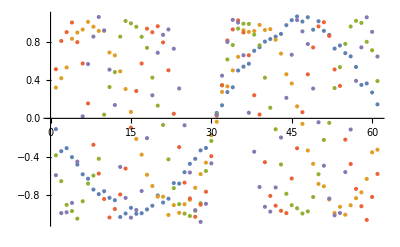

```mathematica
ListPlot[table]
```

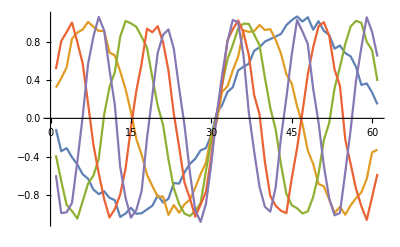

```mathematica
ListPlot[table,Joined->True]
```

```mathematica
ListPlot3D[table]
```

-Graphics3D-

### XLS Example

```mathematica
FileNames["*.xls"]
```

{Apple Licenses down to Version 10.xls,COMPPROS-1340-4902.xls,COMPPROS-1340_Jupyter-iPython_Scholar2.xls,jup&Pyth.xls,Jupyter&iPythonSearches2.xls,Licenses Info by Multiple Parameters Apple.xls,Licenses numbers and configuration Apple.xls,MailingList.xls,SampleLabData.xls}

```mathematica
sampleData=Import["SampleLabData.xls"]⟦1⟧;
Dimensions[sampleData]
```

{19,2}

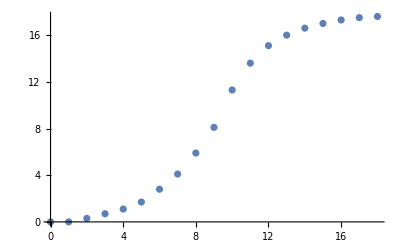

```mathematica
ListPlot[sampleData]
```

Fit a model to the data

```mathematica
model=LinearModelFit[sampleData,{1,x,x^2,x^3},x]
```

FittedModel[0.689132-1.15292 x+0.340389 x^2-0.0125551 x^3]

Visualize the data and the fitted model

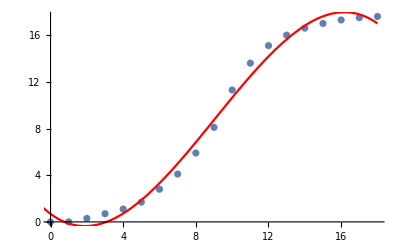

```mathematica
Show[ListPlot[sampleData],Plot[model[x],{x,-5,18},PlotStyle->Red]]
```

### HTML Example

Here is the list of the Big ten Schools

```mathematica
EntityList[LinguisticAssistant]
```

{Indiana University-Bloomington,Michigan State University,Northwestern University,Ohio State University-Main Campus,Pennsylvania State University - Main Campus,Purdue University-Main Campus,Rutgers University-New Brunswick,University of Illinois at Urbana-Champaign,University of Iowa,University of Maryland-College Park,University of Michigan-Ann Arbor,University of Minnesota-Twin Cities,University of Nebraska-Lincoln,University of Wisconsin-Madison}

And you can find the webpages of their football rosters

```mathematica
bigTenUrls={"https://iuhoosiers.com/sports/football/roster","https://msuspartans.com/sports/football/roster","https://nusports.com/sports/football/roster/2020","https://ohiostatebuckeyes.com/sports/m-footbl/roster/","https://gopsusports.com/sports/football/roster","https://purduesports.com/sports/football/roster","https://scarletknights.com/sports/football/roster","https://fightingillini.com/roster.aspx?path=football","https://hawkeyesports.com/sports/football/roster","https://umterps.com/sports/football/roster","https://mgoblue.com/sports/football/roster","https://gophersports.com/sports/football/roster","https://huskers.com/sports/football/roster","https://uwbadgers.com/sports/football/roster"};
```

```mathematica
SystemOpen["https://fightingillini.com/roster.aspx?path=football"]
```

```mathematica
Import["https://fightingillini.com/roster.aspx?path=football","Elements"]
```

{Data,FullData,Hyperlinks,ImageLinks,Images,Plaintext,Source,Title,XMLObject}

You can then Import the data on their current players

```mathematica
nData=Cases[Import[#,"Data"],{_Integer,_String,__String,_Integer,__String},Infinity]&/@bigTenUrls
```

{{{0, Layne, Raheem ,DB,6-1,197,Sr.,Deland, Fla. / Sebastian River},{1, Matthews, Devon ,DB,6-2,202,Jr.,Jacksonville, Fla. / Ribault},{1, Philyor, Whop ,WR,5-11,180,Sr.,Tampa, Fla. / Plant},{2, Hewitt, Jacolby ,WR,6-1,202,R-So.,Cordova, Tenn. / Cordova},{2, Taylor, Reese ,DB,5-11,185,Jr.,Indianapolis, Ind. / Ben Davis},{3, Fryfogle, Ty ,WR,6-2,214,Sr.,Lucedale, Miss. / George County},110,{95, Wracher, Sean ,LS,6-4,223,So.,Akron, Ohio / Saint Ignatius},{96, Murphy, Caleb ,TE,6-4,260,Fr.,Campbellsburg, Ind. / West Washington},{97, Reece, Tramar ,DL,6-4,258,R-Jr.,Clearwater, Fla. / Clearwater},{97, Wellmann, Jake ,LS,6-1,210,Fr.,Indianapolis, Ind. / Warren Central},{98, Johnson, Jerome ,DL,6-3,304,R-Sr.,Bassfield, Miss. / Bassfield},{99, Cardillo, Jack ,K,6-1,180,R-Jr.,Evergreen, Colo. / Evergreen}},{1},{1},8,{1},{1},{1}}
 |  |  |  |

Find Which ones did not return acceptable formats (so we would have to do additional data extraction and cleaning for them)

```mathematica
Position[nData,{}]
```

{{9}}

And ask information about it, like give me all the Quarterbacks in the list

```mathematica
Cases[nData,{__,"QB",__},Infinity]//Grid
```

5 |  Williams II, Dexter  | QB | 6-1 | 208 | Fr. | Macon, Ga. / Mount de Sales Academy |  | 
9 |  Penix Jr., Michael  | QB | 6-3 | 218 | R-So. | Tampa, Fla. / Tampa Bay Tech |  | 
14 |  Tuttle, Jack  | QB | 6-4 | 215 | R-So. | San Marcos, Calif. / Mission Hills | University of Utah | 
15 |  Merrill, Zack  | QB | 5-11 | 209 | R-Fr. | Hobart, Ind. / Andrean |  | 
16 |  Gremel, Grant  | QB | 6-3 | 199 | R-Fr. | Noblesville, Ind. / Noblesville |  | 
25 |  Jontz, Will  | QB | 6-3 | 221 | R-Fr. | Brighton, Mich. / Brighton |  | 
6 |  Theo Day  | QB | 6-5 | 225 | R-So. | Canton, Mich. / Divine Child |  | 
10 |  Payton Thorne  | QB | 6-2 | 210 | R-Fr. | Naperville, Ill. / Naperville Central |  | 
14 |  Noah Kim  | QB | 6-2 | 170 | Fr. | Centreville, Va. / Westfield |  | 
16 |  Eli McLean  | QB | 6-2 | 205 | R-So. | Clarkston, Mich. / Notre Dame Prep |  | 
19 |  Zach Gillespie  | QB | 6-2 | 210 | Fr. | East Lansing, Mich. / Lansing Catholic |  | 
21 |  Andrew Schorfhaar  | QB | 6-2 | 195 | Fr. | DeWitt, Mich. / DeWitt |  | 
7 |  Andrew Marty  | QB | 6-3 | 224 | Jr. | Cincinnati, Ohio / Wyoming |  | 
9 |  Carl Richardson  | QB | 6-4 | 207 | Fy. | Salinas, Calif. / Salinas |  | 
10 |  TJ Green  | QB | 6-2 | 205 | Gr. | Leawood, Kan. / Rockhurst |  | 
12 |  Peyton Ramsey  | QB | 6-2 | 220 | Gr. | Cincinnati, Ohio / Elder |  | 
15 |  Hunter Johnson  | QB | 6-2 | 215 | Jr. | Brownsburg, Ind. / Brownsburg |  | 
16 |  Zac Krause  | QB | 6-3 | 215 | R-Fy. | Olathe, Kan. / Olathe West |  | 
1 | Justin Fields | QB | 6-3 | 228 | Junior | Kennesaw, Ga. | Georgia / Harrison H.S. | 
9 | Jack Miller III | QB | 6-3 | 215 | Freshman | Scottsdale, Ariz. | Chaparral | 
12 | Gunnar Hoak | QB | 6-4 | 215 | Graduate | Dublin, Ohio | UK / Coffman | 
14 | C.J. Stroud | QB | 6-3 | 205 | Freshman | Rancho Cucamonga, Calif. | Rancho Cucamonga | 
17 | Danny Vanatsky | QB | 6-1 | 210 | Junior | Cincinnati, Ohio | Cincinnati Hills Christian Academy | 
18 | J.P. Andrade | QB | 6-2 | 210 | Sophomore | La Verne, Calif. | Bonita | 
19 | Jagger LaRoe | QB | 6-3 | 220 | Sophomore | Colleyville, Texas | Texas A&M / Colleyville Heritage | 
2 |  Micah Bowens  | QB | Fr. | 5-11 | 196 | Las Vegas, Nev. / Bishop Gorman |  | 
7 |  Will Levis  | QB | R-So. | 6-3 | 222 | Madison, Conn. / Xavier |  | 
9 |  Ta'Quan Roberson  | QB | R-Fr. | 5-11 | 195 | Orange, N.J. / DePaul Catholic |  | 
14 |  Sean Clifford  | QB | R-Jr. | 6-2 | 217 | Cincinnati, Ohio / Saint Xavier |  | 
17 |  Mason Stahl  | QB | Fr. | 6-0 | 204 | Pittsburgh, Pa. / Baldwin |  | 
1 |  Michael Alaimo  | Fr. | QB | 6-4 | 215 | Montvale, N.J. / St. Joseph Regional | Exploratory Studies | 
13 |  Jack Plummer  | So. | QB | 6-5 | 220 | Gilbert, Ariz. / Gilbert | Management | 
16 |  Aidan O'Connell  | Jr. | QB | 6-3 | 200 | Long Grove, Ill. / Stevenson | Management | 
17 |  Austin Burton  | Jr. | QB | 6-2 | 200 | Newton, Mass. / | MS Technology Leadership & Innovation | UCLA
19 |  Jack Albers  | R-Fr. | QB | 6-0 | 180 | Louisville, Ky. / | Selling & Sales Management | Dayton
21 |  Andrew Hobson  | Fr. | QB | 6-1 | 210 | Indianapolis, Ind. / Hamilton Southeastern | Management | 
19 |  Austin Albericci  | QB | Jr. | 5-10 | 174 | Closter, N.J. / Demarest |  | 
21 |  Johnny Langan  | QB | Jr. | 6-3 | 223 | Wayne, N.J. / Bergen Catholic |  | 
3 |  Evan Simon  | QB | Fr. | 6-3 | 210 | Mount Joy, Pa. / Manheim Central |  | 
8 |  Artur Sitkowski  | QB | Jr. | 6-5 | 224 | Old Bridge, N.J. / Old Bridge/IMG Academy [Fla.] |  | 
16 |  Cole Snyder  | QB | So. | 6-2 | 194 | Lakewood, N.Y. / Southwestern |  | 
0 |  Noah Vedral  | QB | Sr. | 6-1 | 195 | Wahoo, Neb. / Bishop Neumann |  | 
1 |  Isaiah Williams  | QB | 5-10 | 180 | R-Fr. | St. Louis, Mo. | Trinity Catholic | 
6 |  Deuce Spann  | QB | 6-4 | 195 | Fr. | St. Petersburg, Fla. | Lakewood | 
7 |  Coran Taylor  | QB | 6-2 | 190 | So. | Peoria, Ill. | Peoria | 
12 |  Matt Robinson  | QB | 6-1 | 190 | So. | San Juan Capistrano, Calif. | J Serra Catholic | 
16 |  Josh Beetham  | QB | 6-5 | 235 | Fr. | Yorkville, Ill. | Yorkville | 
18 |  Brandon Peters  | QB | 6-5 | 220 | Sr. | Avon, Ind. | Avon | Michigan
3 |  Taulia Tagovailoa  | QB | 5-11 | 205 | So. | Ewa Beach, HI. / Thompson |  | 
12 |  Lance LeGendre  | QB | 6-1 | 215 | R-Fr. | Animal Science | New Orleans, La. / Warren Easton | 
14 |  David Foust  | QB | 6-4 | 181 | Fr. | Business Marketing | Edgewater, MD / South River | 
17 |  Josh Jackson  | QB | 6-2 | 218 | Sr. | Professional Studies in Technology Entrepreneurship | Ann Arbor, Mich. / Saline | 
18 |  Josh Ettlinger  | QB | 6-0 | 200 | Fr. | Business | Baltimore, MD / Gilman School | 
22 |  Eric Najarian  | QB | 6-4 | 204 | So. | Business | Crofton, Md. / DeMatha Catholic | 
4 |  Dan Villari  | QB | 6-4 | 227 | Fr. | Massapequa, N.Y. / Plainedge |  | 
5 |  Joe Milton  | QB | 6-5 | 243 | Jr. | Pahokee, Fla. / Olympia |  | 
7 |  Peyton Smith  | QB | 6-3 | 190 | Fr. | Ithaca, Mich. / Traverse City Central |  | 
10 |  Dylan McCaffrey  | QB | 6-5 | 220 | Sr. | Castle Rock, Colo. / Valor Christian | Opted out of season | 
12 |  Cade McNamara  | QB | 6-1 | 205 | So. | Reno, Nev. / Damonte Ranch |  | 
15 |  Andy Maddox  | QB | 6-4 | 212 | So. | Prairie Village, Kan. / Shawnee Mission East |  | 
16 |  Ren Hefley  | QB | 6-0 | 197 | So. | Bryant, Ark. / Bryant |  | 
18 |  Max Wittwer  | QB | 6-2 | 205 | Jr. | Utica, Mich. / Eisenhower |  | 
2 |  Tanner Morgan  | QB | 6-2 | 215 | R-Jr. | Union, Ky. / Ryle |  | 
5 |  Zack Annexstad  | QB | 6-3 | 220 | R-So. | Norseland, Minn. / IMG Academy |  | 
11 |  Lonenoa Faoa  | QB | 6-1 | 230 | Fr. | Las Vegas, Nev. / Liberty |  | 
12 |  Cole Kramer  | QB | 6-1 | 205 | R-Fr. | Eden Prairie, Minn. / Eden Prairie High School |  | 
15 |  Jacob Clark  | QB | 6-5 | 225 | R-Fr. | Rockwall, Texas / Rockwall High School |  | 
19 |  Samuel Pickerign  | QB | 6-4 | 230 | R-Jr. | Alpharetta, Ga. / Minnehaha Academy |  | 
2 |  Adrian Martinez  | QB | 6-2 | 220 | Jr. | Fresno, Calif. / Clovis West |  | 
7 |  Luke McCaffrey  | QB | 6-2 | 200 | R-Fr. | Highlands Ranch, Colo. / Valor Christian |  | 
8 |  Logan Smothers  | QB | 6-2 | 190 | Fr. | Muscle Shoals, Ala. / Muscle Shoals |  | 
14 |  Brayden Miller  | QB | 6-1 | 210 | R-Fr. | Kearney, Neb. / Kearney |  | 
18 |  Matt Masker  | QB | 6-1 | 220 | So. | Kearney, Neb. / Kearney Catholic |  | 
2 |  Chase Wolf  | QB | 6-1 | 196 | So. | Cincinnati, Ohio | Saint Xavier | 
5 |  Graham Mertz  | QB | 6-3 | 215 | R-Fr. | Overland Park, Kan. | Blue Valley North | 
12 |  Daniel Wright  | QB | 6-8 | 215 | Fr. | Sergeant Bluff, Iowa | Sergeant Bluff-Luton | 
15 |  Danny Vanden Boom  | QB | 6-5 | 207 | Jr. | Kimberly, Wis. | Kimberly | 
17 |  Jack Coan  | QB | 6-3 | 221 | Sr. | Sayville, N.Y. | Sayville |

# Twitter Project

## Following the MPD DS Class Example

Connect to the Twitter API

```mathematica
twitter=ServiceConnect["Twitter",SaveConnection->True]
```

ServiceObject[…]

Download the tweets made by an account by setting “Username” to the user name

```mathematica
muskTweets=twitter["TweetList","Username"->"elonmusk",MaxItems->5000,"Elements"->"FullData"];
```

```mathematica
Save[FileNameJoin[{Directory[],"muskTweets.mx"}],muskTweets]
```

```mathematica
FileSize[FileNameJoin[{Directory[],"muskTweets.mx"}]]
```

2.05608 MB

```mathematica
Get[FileNameJoin[{Directory[],"muskTweets.mx"}]];
```

```mathematica
RandomSample[muskTweets,5]
```

```mathematica
%[[3]]
```

```mathematica
Normal[%]
```

<|ID→1251663844860063746,Text→@flcnhvy You’d think they’d at least be Wikipedia-level informed about ventilators! It clearly articulates the difference between invasive &amp; non-invasive. It’s very misleading to the public to claim that only the invasive type are “real ventilators”.
https://t.co/wHkAQ9177V,Date→Sat 18 Apr 2020 18:08:10GMT-6,Hashtags→{},Location→Missing[NotAvailable],Username→elonmusk,Name→Elon Musk,ProfileImageThumbnail→URL[https://pbs.twimg.com/profile_images/1295975423654977537/dHw9JcrK_normal.jpg],RetweetCount→96,FavoriteCount→1035,URL→URL[https://twitter.com/elonmusk/status/1251663844860063746]|>

```mathematica
txt=%["Text"]
```

@flcnhvy You’d think they’d at least be Wikipedia-level informed about ventilators! It clearly articulates the difference between invasive &amp; non-invasive. It’s very misleading to the public to claim that only the invasive type are “real ventilators”.
https://t.co/wHkAQ9177V

```mathematica
StringCases[txt,"@"~~u:(LetterCharacter|DigitCharacter|"_")..~~(WhitespaceCharacter|PunctuationCharacter|EndOfString):>u]
```

{flcnhvy}

```mathematica
getUserMentions[tweet_Association]:=Module[{modifiedTweet=tweet},AssociateTo[modifiedTweet,"Usermentions"->Flatten[StringCases[tweet["Text"],"@"~~u:(LetterCharacter|DigitCharacter|"_")..~~(WhitespaceCharacter|PunctuationCharacter|EndOfString):>u]]]
]
```

```mathematica
tesTweetAssoc=Normal@RandomChoice[muskTweets]
```

<|ID→1328734675544707072,Text→@DJSnM @Erdayastronaut @CharlesNOtrumps @rweb11742 Absolutely. Production/testing of rocket engines is over 90% of the problem. This is true in general. For cars, production is over 99% of the problem. That 1% inspiration is very important, but it’s less than 1% of the pain.,Date→Tue 17 Nov 2020 10:20:08GMT-6,Hashtags→{},Location→Missing[NotAvailable],Username→elonmusk,Name→Elon Musk,ProfileImageThumbnail→URL[https://pbs.twimg.com/profile_images/1295975423654977537/dHw9JcrK_normal.jpg],RetweetCount→54,FavoriteCount→1876,URL→URL[https://twitter.com/elonmusk/status/1328734675544707072]|>

```mathematica
getUserMentions[tesTweetAssoc]
```

<|ID→1328734675544707072,Text→@DJSnM @Erdayastronaut @CharlesNOtrumps @rweb11742 Absolutely. Production/testing of rocket engines is over 90% of the problem. This is true in general. For cars, production is over 99% of the problem. That 1% inspiration is very important, but it’s less than 1% of the pain.,Date→Tue 17 Nov 2020 10:20:08GMT-6,Hashtags→{},Location→Missing[NotAvailable],Username→elonmusk,Name→Elon Musk,ProfileImageThumbnail→URL[https://pbs.twimg.com/profile_images/1295975423654977537/dHw9JcrK_normal.jpg],RetweetCount→54,FavoriteCount→1876,URL→URL[https://twitter.com/elonmusk/status/1328734675544707072],Usermentions→{DJSnM,Erdayastronaut,CharlesNOtrumps,rweb11742}|>

```mathematica
muskTweets=Dataset[getUserMentions/@Normal@muskTweets];
```

```mathematica
Save[FileNameJoin[{Directory[],"muskTweetsWithUserMentions.mx"}],muskTweets]
```

```mathematica
FileSize[FileNameJoin[{Directory[],"muskTweetsWithUserMentions.mx"}]]
```

2.23142 MB

## Explore

```mathematica
Get[FileNameJoin[{Directory[],"muskTweetsWithUserMentions.mx"}]];
```

```mathematica
muskTweets
```

Dataset[<>]

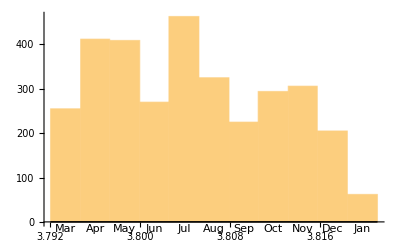

```mathematica
muskTweets[DateHistogram[#,"Month"]&,"Date"]
```

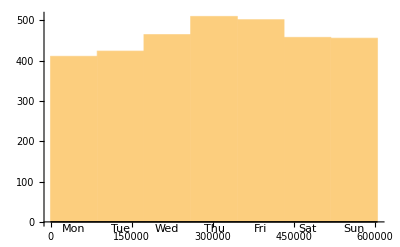

```mathematica
DateHistogram[muskTweets[All,"Date"],"Day",DateReduction->"Week"]
```

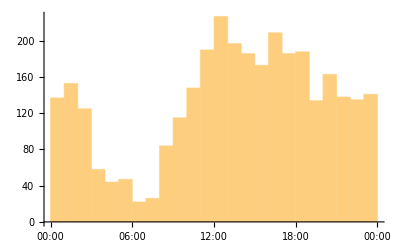

```mathematica
DateHistogram[muskTweets[All,"Date"],"Hour",DateReduction->"Day"]
```

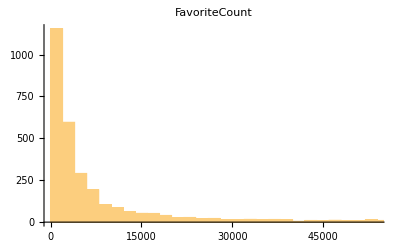

```mathematica
muskTweets[Histogram[#,(*PlotRange->All,*)PlotLabel->"FavoriteCount"]&,"FavoriteCount"]
```

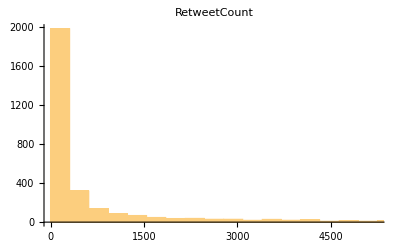

```mathematica
muskTweets[Histogram[#,(*PlotRange->All,*)PlotLabel->"RetweetCount"]&,"RetweetCount"]
```

```mathematica
muskTweets[Max,"FavoriteCount"]
```

1613315

```mathematica
muskTweets[Max,"RetweetCount"]
```

308846

```mathematica
ReverseSortBy[muskTweets,"FavoriteCount"][[;;5]]
```

```mathematica
Reverse[SortBy[muskTweets,"RetweetCount"]][[;;5]]
```

```mathematica
muskTweets[All,"Hashtags"]
```

```mathematica
muskTweets[Select[#,#≠{}&]&,"Hashtags"]
```

```mathematica
muskTweets[Flatten/*Counts/*ReverseSort,"Hashtags"]
```

```mathematica
muskTweets[Flatten/*Counts/*ReverseSort,"Usermentions"]
```

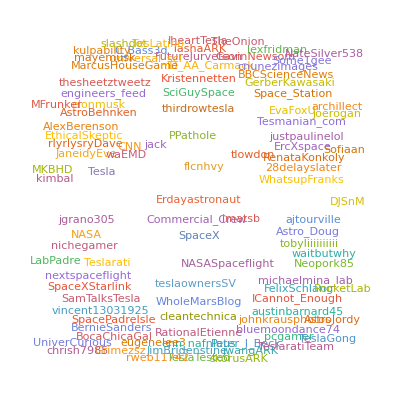

```mathematica
muskTweets[Flatten/* WordCloud,"Usermentions"]
```

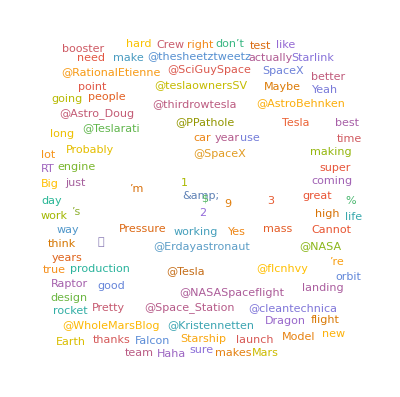

```mathematica
muskTweets[Flatten/*StringJoin/*WordCloud,"Text"]
```

```mathematica
cleanText[txt_String]:=DeleteStopwords[
StringDelete[txt,{"&amp","$","%",DigitCharacter}]]
```

```mathematica
cleanTextMentions[txt_String]:=DeleteStopwords[
StringDelete[txt,{"&amp","$","%",DigitCharacter,"@"~~Except[WhitespaceCharacter]..~~WhitespaceCharacter}]]
```

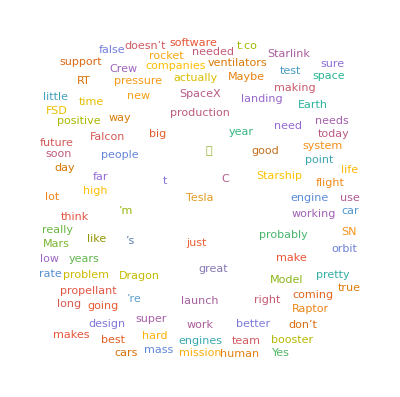

```mathematica
muskTweets[Flatten/*StringJoin/*WordCloud,"Text",cleanTextMentions]
```

```mathematica
mentionedUsers=Normal[muskTweets[Flatten/*DeleteDuplicates,"Usermentions"]];
```

```mathematica
Length[mentionedUsers]
```

1321

Do not run the following

```mathematica
twitter["UserData","Username"->#]&/@mentionedUsers(*issues*)
```

Twitter will cap the above as the max number of calls on a 15 min window is 180

```mathematica
iterations=Ceiling[Length[mentionedUsers]/180]
```

8

We will have to make 8 calls which is not too bad ~ 2 hours

Let us make a function

```mathematica
getTwitterData[request_String,userNames_List]:=twitter[request,"Username"->#]&/@userNames;
```

And setup the task

```mathematica
i=1;
data={};
SessionSubmit[
ScheduledTask[
AppendTo[data,getTwitterData["UserData",Partition[mentionedUsers,UpTo[180]]⟦i++⟧]],
{Quantity[16,"Minutes"],iterations}],
HandlerFunctions-><|"TaskStatusChanged"->(Print["Task status: ",#TaskStatus]&)|>,HandlerFunctionsKeys->{"TaskStatus"}]
```

TaskObject[<|TaskUUID -> aa3fb5b6-a68a-4e15-9992-73638a3f21c3, TaskEnvironment -> Session, TaskType -> Scheduled, EvaluationExpression :> AppendTo[data, getTwitterData[UserData, Partition[mentionedUsers, UpTo[180]][[i++]]]], Schedule -> <|Type -> Repeated, TotalRunCount -> 8, <<2>>, EndDate -> Infinity|>, <<1>>, HandlerFunctionsKeys -> {TaskStatus}, AutoRemove -> True|>]

```mathematica
mentionedUsersData=data;
```

```mathematica
RandomSample[mentionedUsersData[[1]],5]
```

```mathematica
Save[FileNameJoin[{Directory[],"mentionedUserData.mx"}],mentionedUsersData]
```

```mathematica
Get[FileNameJoin[{Directory[],"mentionedUserData.mx"}]];
```

```mathematica
Flatten[mentionedUsersData]//Length
```

1321

```mathematica
successMentionedUsersData=Dataset[DeleteCases[Flatten[mentionedUsersData],Except[_Association]]];
```

```mathematica
successMentionedUsersData//Length
```

1227

```mathematica
Save[FileNameJoin[{Directory[],"successMentionedUsersData.mx"}],successMentionedUsersData]
```

```mathematica
Get[FileNameJoin[{Directory[],"successMentionedUsersData.mx"}]];
```

```mathematica
RandomSample[successMentionedUsersData,5]
```

The line below takes time

```mathematica
locations=Interpreter["ComputedLocation"]/@Normal@successMentionedUsersData[All,"Location"];
```

Interpreter::cut: Warning: the full computation may take too long, only returning the first result.

General::stop: Further output of Interpreter::cut will be suppressed during this calculation.

```mathematica
cleanLocations=DeleteCases[locations,Except[GeoPosition[{_,_}]]];
```

```mathematica
Save[FileNameJoin[{Directory[],"cleanLocations.mx"}],cleanLocations]
```

```mathematica
Get[FileNameJoin[{Directory[],"cleanLocations.mx"}]];
```

```mathematica
GeoListPlot[cleanLocations]
```

-Graphics-

```mathematica
GeoHistogram[cleanLocations,PlotLegends->Automatic]
```

-Graphics-

```mathematica
First[SortBy[cleanLocations,Part[#,1,1]&]]
```

GeoPosition[{-81.5,0.}]

```mathematica
GeoNearest[Entity["Country"],GeoPosition[{-81.5,0.}]]
```

{Antarctica}

```mathematica
Save[FileNameJoin[{Directory[],"locations.mx"}],locations]
```

```mathematica
Get[FileNameJoin[{Directory[],"locations.mx"}]];
```

```mathematica
successMentionedUsersData[[Position[locations,GeoPosition[{-81.5,0.}]][[1]]]]
```

Perhaps we are interested in pulling the Hashtag data from those mentioned

```mathematica
i=1;
data={};
SessionSubmit[
ScheduledTask[
AppendTo[data,getTwitterData["UserHashtags",Partition[mentionedUsers,UpTo[180]]⟦i++⟧]],
{Quantity[16,"Minutes"],iterations}],
HandlerFunctions-><|"TaskStatusChanged"->(Print["Task status: ",#TaskStatus]&)|>,HandlerFunctionsKeys->{"TaskStatus"}]
```

Task status: Running

TaskObject[<|TaskUUID -> 9f6c81e6-73e9-4d32-a77e-8157e26340f1, TaskEnvironment -> Session, TaskType -> Scheduled, EvaluationExpression :> AppendTo[data, getTwitterData[UserHashtags, Partition[mentionedUsers, UpTo[180]][[i++]]]], Schedule -> <|Type -> Repeated, TotalRunCount -> 8, <<2>>, EndDate -> Infinity|>, <<1>>, HandlerFunctionsKeys -> {TaskStatus}, AutoRemove -> True|>]

```mathematica
Length/@data
```

{180,180,180,180,180,180,180,53}

```mathematica
mentionedUserHashtags=Flatten[data,1];
```

```mathematica
Save[FileNameJoin[{Directory[],"mentionedUserHashtags.mx"}],mentionedUserHashtags]
```

```mathematica
Get[FileNameJoin[{Directory[],"mentionedUserHashtags.mx"}]];
```

ServiceExecute::nouser: No user matches for specified terms.

General::stop: Further output of ServiceExecute::nouser will be suppressed during this calculation.

ServiceExecute::unauth: Not authorized.

General::stop: Further output of ServiceExecute::unauth will be suppressed during this calculation.

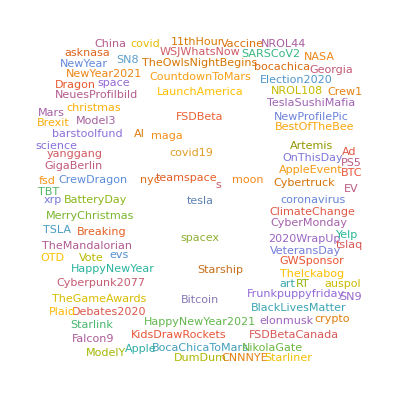

```mathematica
Flatten[mentionedUserHashtags]//WordCloud
```

```mathematica
i=1;
data={};
SessionSubmit[ScheduledTask[AppendTo[data,getTwitterData["UserMentions",Partition[mentionedUsers,UpTo[180]][[i++]]]],{Quantity[16,"Minutes"],iterations}]]
```

TaskObject[<|TaskUUID -> 1cc2b4f3-3471-4257-9ae7-9e27c34c3d9f, TaskEnvironment -> Session, TaskType -> Scheduled, <<3>>, HandlerFunctionsKeys -> {Task, TaskUUID, TaskType, TaskStatus, TaskEnvironment, HandlerFunctions, HandlerFunctionsKeys, EventName, EvaluationExpression, <<4>>, Re<<12>>unt, NextScheduledTime, TotalRunCount, MessageOutput, PrintOutput}, AutoRemove -> True|>]

```mathematica
mentionedUserUserMentions=Cases[Thread[mentionedUsers->Join@@data],Rule[a_,b_]/;Head[b]==List];
```

```mathematica
Save["mentionedUserUserMentions.mx",mentionedUserUserMentions]
```

```mathematica
Get["mentionedUserUserMentions.mx"];
```

```mathematica
Association[RandomSample[mentionedUserUserMentions,5]]//Dataset
```

```mathematica
Cases[mentionedUserUserMentions,Rule[a_,b_]/;Length[b]==0]
```

{realDonaldTrump→{},valleyhack→{},verified→{},xkcdComic→{},koro_alex→{},Barnes_Law→{},Alfzeta→{},ISS_Re→{},ThingsWork→{},Apple→{},NASAPsyche→{}}

```mathematica
getTwitterData["UserMentions",{"realDonaldTrump"}]
```

{{SenTedCruz,HawleyMO,Jim_Jordan,senatemajldr,GOPLeader,BreitbartNews,AmyKremer,LizWillis_,america1stwomen,RSBNetwork,AmyKremer,KLoeffler,Perduesenate,SenatorLoeffler,sendavidperdue,AmyKremer,AmyKremer,AmyKremer,AmyKremer,realMikeLindell}}

```mathematica
getTwitterData["UserMentions",Cases[mentionedUserUserMentions,Rule[a_,b_]:>a/;Length[b]==0]]
```

{{SenTedCruz,HawleyMO,Jim_Jordan,senatemajldr,GOPLeader,BreitbartNews,AmyKremer,LizWillis_,america1stwomen,RSBNetwork,AmyKremer,KLoeffler,Perduesenate,SenatorLoeffler,sendavidperdue,AmyKremer,AmyKremer,AmyKremer,AmyKremer,realMikeLindell},{},{},{},{},{},{},{},{},{},{}}

```mathematica
mentionedUserUserMentions=Normal[Association[Association[mentionedUserUserMentions],"realDonaldTrump"->First@getTwitterData["UserMentions",{"realDonaldTrump"}]]]
```

```mathematica
edges=Cases[mentionedUserUserMentions,Rule[a_,b_]/;Length[b]≠0]
```

{elonmusk→{RGVaerialphotos,SpaceX,Gfilche,flcnhvy,Tesla,newscientist,comma_ai,PPathole,jack,flcnhvy,smvllstvrs,ErcXspace,jack,Erdayastronaut,Erdayastronaut,flcnhvy,ErcXspace,ICannot_Enough,AloysiusFekete,RationalEtienne},1205,oyvi00i→{NyrAutomobile,grandayy,NyrAutomobile,grandayy,grandayy,Vebteo,8,Fact,imermot,TailosiveNet,StianTStaysman,tyler420699,TGdog}}
 |  |  |  |

```mathematica
AppendTo[edges,"elonmusk"->mentionedUsers];
```

#### Graph

```mathematica
graph=Flatten[Thread[#⟦1⟧->DeleteDuplicates[#[[2]]]]&/@edges]
```

{elonmusk->RGVaerialphotos,elonmusk->SpaceX,elonmusk->Gfilche,elonmusk->flcnhvy,elonmusk->Tesla,elonmusk->newscientist,elonmusk->comma_ai,elonmusk->PPathole,elonmusk->jack,18301,elonmusk->TwitterSupport,elonmusk->LeeHudson_,elonmusk->newscientist,elonmusk->Foxfire40900590,elonmusk->JakeTheHuman28,elonmusk->j_brorsson,elonmusk->Bryr32,elonmusk->oyvi00i}
 |  |  |  |

```mathematica
Graph[graph]
```

```mathematica
simpleGraph=SimpleGraph[graph]
```

```mathematica
inDegrees=SortBy[#->VertexInDegree[simpleGraph,#]&/@VertexList[simpleGraph],Last]
```

{015watson→1,029_MB→1,0K_ultra→1,0xa000→1,0x_brian→1,1000genes→1,100xcode→1,106Euan→1,10News→1,10NewsAarons→1,116jerome→1,11LunarLuster11→1,11thHour→1,11995,SawyerMerritt→42,realDonaldTrump→48,NASASpaceflight→50,teslaownersSV→53,ErcXspace→54,Kristennetten→59,NASA→59,flcnhvy→61,28delayslater→63,Erdayastronaut→80,SpaceX→140,Tesla→188,elonmusk→461}
 |  |  |  |

```mathematica
inDegree15OrMore=ReverseSort[Select[Association[inDegrees],#>14&]];
```

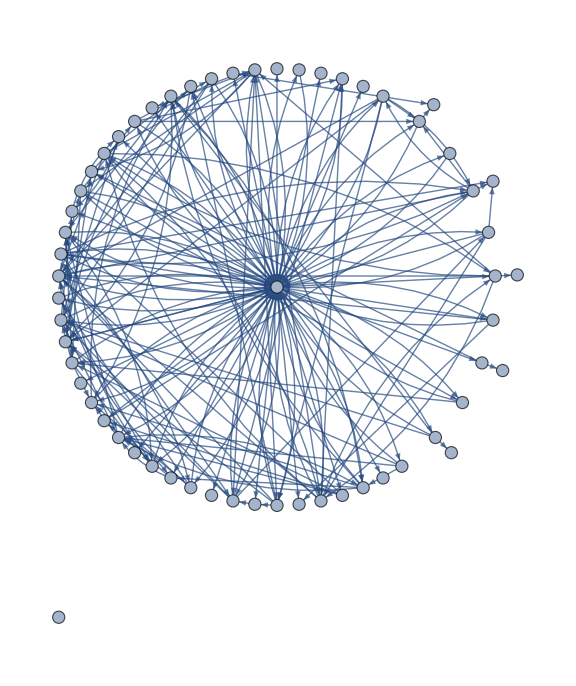

```mathematica
subG=Subgraph[simpleGraph,Keys@inDegree15OrMore,VertexLabels->Placed["Name",Tooltip],GraphLayout->"BalloonEmbedding",ImageSize->Large]
```

#### End of Graph

```mathematica
highlightedSubgraph=HighlightGraph[subG,{VertexList[subG],Property["elonmusk",VertexSize->5]},VertexSize->Thread[Drop[VertexList[subG],1]->2Rescale[Drop[DegreeCentrality[subG],1]]],ImageSize->Large]
```

-Graphics-

```mathematica
Get[FileNameJoin[{Directory[],"muskTweets.mx"}]];
```

```mathematica
muskTweets
```

Dataset[<>]

```mathematica
teslaTweets=muskTweets[Select[StringContainsQ[#Text,"Tesla"|"tesla"]&],All]
```

Dataset[<>]

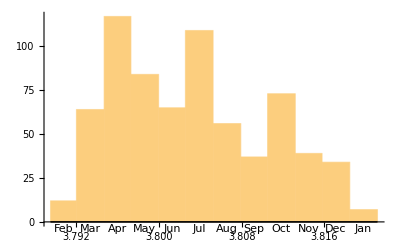

```mathematica
teslaTweets[DateHistogram[#,"Month"]&,"Date"]
```

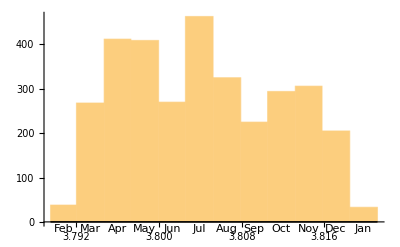

```mathematica
muskTweets[DateHistogram[#,"Month"]&,"Date"]
```

```mathematica
tweetsJuly=muskTweets[Select[IntervalMemberQ[DateInterval[{DateObject[{2020, 7, 1}],DateObject[{2020,7,31}]}],#Date]&],All];
```

```mathematica
tweetsApril=muskTweets[Select[IntervalMemberQ[DateInterval[{DateObject[{2020, 3, 1}],DateObject[{2020,3,30}]}],#Date]&],All];
```

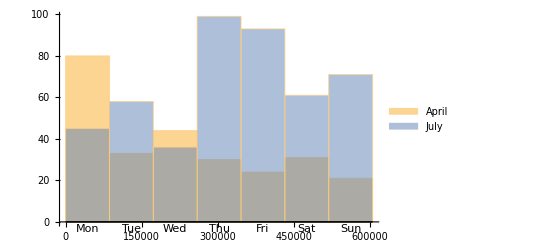

```mathematica
DateHistogram[{tweetsApril[All,"Date"],tweetsJuly[All,"Date"]},"Day",DateReduction->"Week",LabelingFunction->Tooltip,ChartLegends->{"April","July"}]
```

```mathematica
teslaTweetsJuly=teslaTweets[Select[IntervalMemberQ[DateInterval[{DateObject[{2020, 7, 1}],DateObject[{2020,7,31}]}],#Date]&],All];
```

```mathematica
teslaTweetsApril=teslaTweets[Select[IntervalMemberQ[DateInterval[{DateObject[{2020, 3, 1}],DateObject[{2020,7,30}]}],#Date]&],All];
```

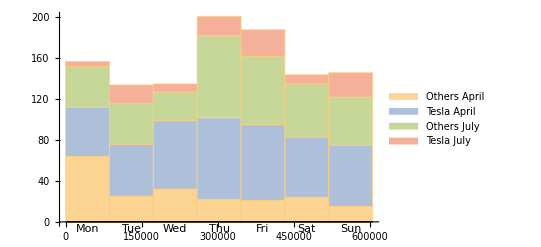

```mathematica
DateHistogram[{
Complement[tweetsApril[All,"Date"],teslaTweetsApril[All,"Date"]],
teslaTweetsApril[All,"Date"],
Complement[tweetsJuly[All,"Date"],teslaTweetsJuly[All,"Date"]],
teslaTweetsJuly[All,"Date"]
},
"Day",DateReduction->"Week",
LabelingFunction->Tooltip,
ChartLayout->"Stacked",
ChartLegends->{"Others April","Tesla April","Others July","Tesla July"}]
```

```mathematica
days=DateDifference@@Normal[muskTweets[{-1,1},"Date"]]
```

322.988 days

```mathematica
num/days
```

10.0561 per day

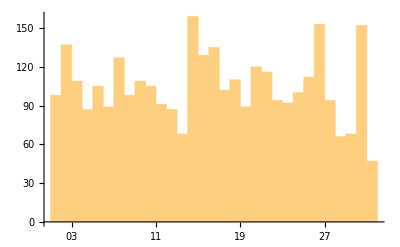

```mathematica
muskTweets[DateHistogram[#,"Day",DateReduction->"Month"]&,"Date"]
```

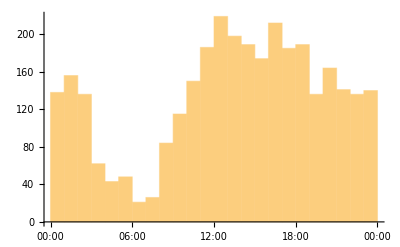

```mathematica
muskTweets[DateHistogram[#,"Hour",DateReduction->"Day"]&,"Date"]
```

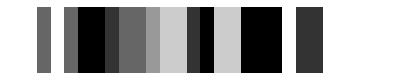

```mathematica
ArrayPlot[{RandomInteger[5,24]}]
```

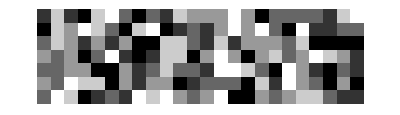

```mathematica
ArrayPlot[RandomInteger[5,{7,24}]]
```

```mathematica
LinguisticAssistant
```

```mathematica
weeklyBuzz[tweetsData_,n_:1]:=Module[{daysOfWeek={Monday,Tuesday,Wednesday,Thursday,Friday,Saturday,Sunday},dayOfWeekCounts,dayOfWeekCountsSummary,dailyByHourTweets},
dayOfWeekCounts=KeyTake[(KeySort[GroupBy[#1,First->Rest]]&)/@GroupBy[({DateObject[#1⟦1⟧]["DayName"],DateObject[#1⟦1⟧]["Hour"],#1⟦2⟧,#1⟦3⟧}&)/@Normal[tweetsData[All,{"Date","RetweetCount","FavoriteCount"}]],First->Rest],daysOfWeek];
dayOfWeekCountsSummary=(Merge[{Length/@#1,Total/@#1},Flatten]&)/@dayOfWeekCounts;
(AssociateTo[dayOfWeekCountsSummary[#1],Table[i->{0,0,0},{i,Complement[Range[1,24],Keys[dayOfWeekCountsSummary[#1]]]}]]&)/@Keys[dayOfWeekCountsSummary];
AssociateTo[dayOfWeekCountsSummary,Thread[Complement[daysOfWeek,Keys[dayOfWeekCountsSummary]]->Association[Table[i->{0,0,0},{i,24}]]]];
dailyByHourTweets = ArrayPlot[ Map[#1⟦n⟧&,(Values[KeySort[dayOfWeekCountsSummary[#1]]]&)/@daysOfWeek,{2}],PlotRange->Full,ColorFunctionScaling->True,Mesh->True,Frame->True,FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->{{MapIndexed[{#2⟦1⟧,#1}&,daysOfWeek],None},{Range[24],None}},
ImageSize->Full,
PlotLabel->"elonmusk Tweets"<>
Switch[n,1,"",2," Retweeted",3," Liked"]<>" ("<>DateString[tweetsData[Min,"Date"],{"DateShort"}]<>" to"<>DateString[tweetsData[Max,"Date"],{"DateShort"}]<>")",
PlotLegends->Placed[Automatic,Below]]]
```

```mathematica
lastWeekEnd=DatePlus[DateObject[Today,"Second"],{-1,Monday}]
```

Second: Mon 4 Jan 2021 00:00:00GMT-6

```mathematica
lastWeekBegin=DatePlus[lastWeekEnd,{-1,"Week"}]
```

Second: Mon 28 Dec 2020 00:00:00GMT-6

```mathematica
tweetsLastWeek=muskTweets[Select[#Date≥lastWeekBegin&&#Date<lastWeekEnd&],All]
```

```mathematica
weeklyBuzz[tweetsLastWeek]
```

-Graphics-

```mathematica
weeklyBuzz[tweetsLastWeek,2]
```

-Graphics-

```mathematica
weeklyBuzz[tweetsLastWeek,3]
```

-Graphics-

```mathematica
ReverseSortBy[muskTweets,#["RetweetCount"]&]
```

Dataset[<>]

```mathematica
retweetCountOutlierThreshold=30000;
```

```mathematica
trainTweets=muskTweets[Select[#Date<DateObject["Nov 2020","Second"]&&#RetweetCount<=retweetCountOutlierThreshold&],All];
```

```mathematica
testTweets=muskTweets[Select[#Date≥ DateObject["Nov 2020","Second"]&&#Date<Today&&#RetweetCount<retweetCountOutlierThreshold&],All];
```

```mathematica
Length/@{trainTweets,testTweets}
```

{2645,536}

```mathematica
p=Predict[Thread[{Normal@trainTweets[All,"Date"],Normal@trainTweets[All,"Text",cleanText]}]->Normal@trainTweets[All,"RetweetCount"],FeatureExtractor->{1->"NumericVector",2-> "TFIDF"}]
```

PredictorFunction[…]

```mathematica
Export[FileNameJoin[{Directory[],"predictor.wmlf"}],p]
```

C:\Users\santiagoc\Documents\predictor.wmlf

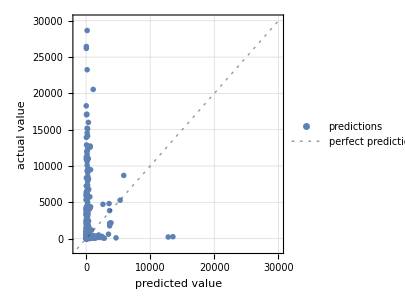

```mathematica
pm=PredictorMeasurements[p,Thread[Thread[{Normal[testTweets[All,"Date"]],Normal[testTweets[All,"Text",cleanText]]}]->Normal[testTweets[All,"RetweetCount"]]]];
pm["ComparisonPlot"]
```

```mathematica
retweetCandidates=testTweets[Select[#RetweetCount≤500&&Round@p[{#Date,cleanText[#Text]}]≥10000&],<|"ActualRetweets"->#RetweetCount,
"PredictedRetweets"->Round@p[{#Date,cleanText[#Text]}],
"Hashtags"->#Hashtags,
"Text"->#Text,"Date"->#Date|>&]
```

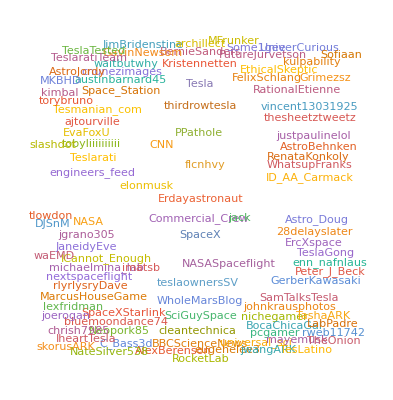

```mathematica
WordCloud[muskTweets[Flatten,"Usermentions"]]
```

```mathematica
rankedMentions=muskTweets[Flatten/*Counts/*ReverseSort,"Usermentions"]
```

```mathematica
KeySelect[muskTweets[Flatten/*Counts/*ReverseSort,"Usermentions"],StringMatchQ[#,___~~"Tesla"~~___,IgnoreCase->True]&]
```

```mathematica
daysBegin = DateObject["Dec 2020","Second"];
daysEnd = DatePlus[daysBegin,{1,"Month"}];
(*daysBegin+Quantity[1,"Month"]*)
decTweets = muskTweets[Select[#Date≥daysBegin && #Date ≤daysEnd &],All]
```

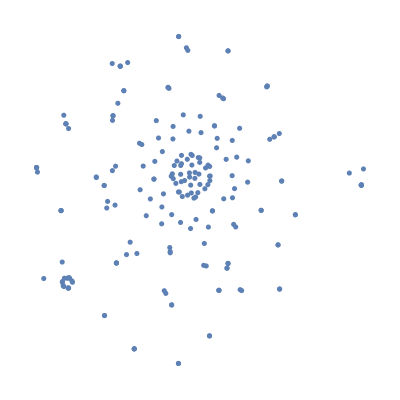

```mathematica
FeatureSpacePlot[decTweets[All,"Usermentions"]]
```

```mathematica
FeatureSpacePlot[decTweets[StringSplit/*Flatten/*DeleteDuplicates,"Text",cleanText],
FeatureExtractor->NetModel["GloVe 50-Dimensional Word Vectors Trained on Tweets"]]
```

-Graphics-

```mathematica
wordVectors = FeatureExtract[decTweets[All,"Text",cleanText],"WordVectors"];
```

```mathematica
tweetWordCentroids = DeleteCases[Thread[Total/@FeatureExtract[decTweets[All,"Text",cleanText],"WordVectors"]->Normal[decTweets[All,"Text",cleanText]]],0->___];
```

#### Segue

```mathematica
tweetWordCentroids[[184]]
```

0→

```mathematica
decTweets[[184]]["Text"]
```

100

```mathematica
FullForm@%
```

"100"

```mathematica
Select[Keys[tweetWordCentroids],Length[#]≠50&]
```

{0}

```mathematica
Position[Keys[tweetWordCentroids],0]
```

{{184}}

```mathematica
Manipulate[Part[tweetWordCentroids,n],{n,1,Length[tweetWordCentroids],1}]
```

```mathematica
Length[tweetWordCentroids]
```

205

```mathematica
DeleteCases[tweetWordCentroids,{0->_}]
```

{1}
 |  |  |  |

```mathematica
Length@%
```

205

#### End Segue

```mathematica
features2D=Thread[DimensionReduce[Keys[tweetWordCentroids],2]->Values[tweetWordCentroids]];
```

```mathematica
First@features2D
```

{-7.35194,-0.398141}→@PPathole Dojo isn’t needed,   make self-driving better.  isn’t    safer  human drivers, Autopilot ultimately needs      times safer  human drivers.

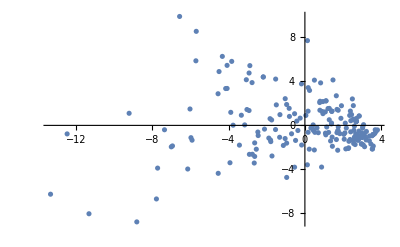

```mathematica
ListPlot[MapThread[Tooltip[#1,#2]&,{Keys@features2D,Values@features2D}]]
```

```mathematica
clusters=FindClusters[features2D[[All,1]]];
```

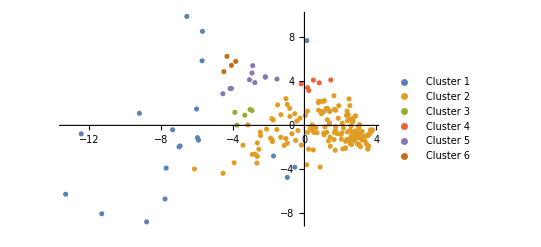

```mathematica
ListPlot[clusters,PlotLegends->Table["Cluster "<>ToString[i],{i,Length[clusters]}]]
```

```mathematica
Length/@FindClusters[features2D]
```

{20,159,5,6,10,4}

```mathematica
clusters=FindClusters[Thread[Total/@FeatureExtract[decTweets[All,"Text",cleanText],"WordVectors"]->Normal[decTweets[All,"Text",cleanText]]],2,Method-> "Agglomerate"];
```

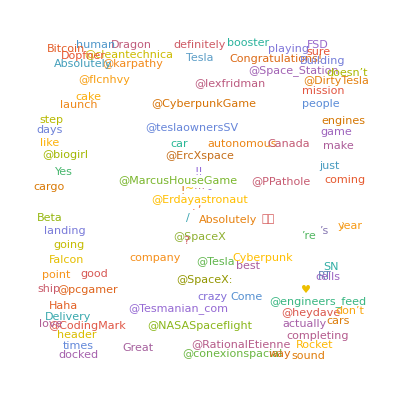
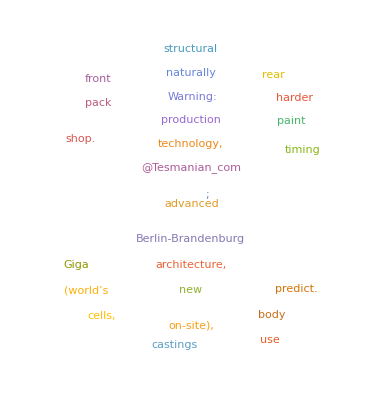

```mathematica
WordCloud/@(Flatten[StringSplit[#]]&/@clusters)
```

```mathematica
labels=Classify["Sentiment",decTweets[All,"Text"]]
```

{Negative,Positive,Neutral,Positive,Positive,Neutral,Positive,Positive,Positive,Positive,Positive,Neutral,Positive,Negative,Positive,Neutral,Positive,Neutral,Neutral,Negative,Negative,Positive,Negative,Neutral,Negative,Negative,Positive,Positive,Positive,Positive,Positive,Neutral,Positive,Neutral,Neutral,Positive,Negative,Positive,Neutral,Positive,Negative,Neutral,Negative,Positive,Positive,Positive,Negative,Positive,Positive,Positive,Negative,Positive,Positive,Positive,Positive,Neutral,Negative,Positive,Negative,Neutral,Negative,Positive,Positive,Positive,Negative,Positive,Neutral,Neutral,Negative,Positive,Neutral,Negative,Positive,Positive,Positive,Neutral,Neutral,Positive,Negative,Positive,Negative,Positive,Neutral,Positive,Positive,Negative,Positive,Neutral,Neutral,Positive,Positive,Positive,Positive,Negative,Negative,Neutral,Neutral,Positive,Negative,Positive,Negative,Positive,Positive,Neutral,Negative,Positive,Positive,Neutral,Positive,Negative,Positive,Neutral,Neutral,Neutral,Neutral,Positive,Neutral,Positive,Positive,Positive,Negative,Positive,Neutral,Negative,Positive,Positive,Negative,Neutral,Negative,Negative,Negative,Positive,Neutral,Positive,Positive,Neutral,Positive,Neutral,Neutral,Positive,Neutral,Positive,Positive,Neutral,Neutral,Neutral,Neutral,Neutral,Neutral,Neutral,Negative,Positive,Negative,Neutral,Positive,Positive,Neutral,Neutral,Positive,Positive,Positive,Neutral,Positive,Positive,Positive,Neutral,Positive,Positive,Neutral,Neutral,Positive,Neutral,Positive,Positive,Positive,Neutral,Neutral,Positive,Positive,Positive,Neutral,Positive,Negative,Neutral,Neutral,Positive,Neutral,Neutral,Positive,Neutral,Positive,Positive,Positive,Neutral,Negative,Positive,Positive,Positive,Negative,Neutral,Positive,Neutral,Neutral,Positive,Positive}

```mathematica
PieChart[Counts[Classify["Sentiment",decTweets[All,"Text"]]],ChartLabels->Placed[Automatic,"RadialCallout"]]
```

-Graphics-

```mathematica
Cases[({#1->Classify["Sentiment",cleanText[#1]]}&)/@decTweets[All,"Text"],{_->"Negative"}]
```

```mathematica
teslaTweets=muskTweets[Select[StringContainsQ[#Text,"Tesla"]&],"Text"]
```

```mathematica
Length[teslaTweets]
```

510

```mathematica
nonTesla=RandomSample[muskTweets[Select[!StringMatchQ[#Text,__~~"data"~~__,IgnoreCase->True]&],"Text"],2 Length[teslaTweets]]
```

```mathematica
teslaClassifier = Classify[<|"Tesla"->Normal[teslaTweets],"NonTesla"->Normal[nonTesla]|>,Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
teslaLabels=<|"PredictedLabel"->teslaClassifier[cleanText[#["Text"]]],"Usermentions"->#["Usermentions"],"Text"->#["Text"]|>&/@Normal@decTweets[All,{"Usermentions","Text"}];
```

```mathematica
PieChart[Counts[#["PredictedLabel"]&/@teslaLabels],ChartLabels->Automatic]
```

-Graphics-

```mathematica
Dataset[teslaLabels][GroupBy[#PredictedLabel&]]
```

#### More Graphs

```mathematica
Get[FileNameJoin[{Directory[],"MentionedUserUserMentions.mx"}]]
```

{elonmusk→{RGVaerialphotos,SpaceX,Gfilche,flcnhvy,Tesla,newscientist,comma_ai,PPathole,jack,flcnhvy,smvllstvrs,ErcXspace,jack,Erdayastronaut,Erdayastronaut,flcnhvy,ErcXspace,ICannot_Enough,AloysiusFekete,RationalEtienne},1216,oyvi00i→{NyrAutomobile,grandayy,NyrAutomobile,grandayy,grandayy,Vebteo,Vebteo,6,NEWSLEAKSGTAS,Fact,imermot,TailosiveNet,StianTStaysman,tyler420699,TGdog}}
 |  |  |  |

```mathematica
edges=Select[mentionedUserUserMentions,!SameQ[#[[2]],Null]&]
```

{elonmusk→{RGVaerialphotos,SpaceX,Gfilche,flcnhvy,Tesla,newscientist,comma_ai,PPathole,jack,flcnhvy,smvllstvrs,ErcXspace,jack,Erdayastronaut,Erdayastronaut,flcnhvy,ErcXspace,ICannot_Enough,AloysiusFekete,RationalEtienne},1216,oyvi00i→{NyrAutomobile,grandayy,NyrAutomobile,grandayy,grandayy,Vebteo,Vebteo,6,NEWSLEAKSGTAS,Fact,imermot,TailosiveNet,StianTStaysman,tyler420699,TGdog}}
 |  |  |  |

```mathematica
AppendTo[edges,"elonmusk"->Keys[mentionedUserUserMentions]]
```

{elonmusk→{RGVaerialphotos,SpaceX,Gfilche,flcnhvy,Tesla,newscientist,comma_ai,PPathole,jack,flcnhvy,smvllstvrs,ErcXspace,jack,Erdayastronaut,Erdayastronaut,flcnhvy,ErcXspace,ICannot_Enough,AloysiusFekete,RationalEtienne},1217,elonmusk→{elonmusk,jack,flcnhvy,smvllstvrs,ErcXspace,Erdayastronaut,1206,newscientist,Foxfire40900590,JakeTheHuman28,j_brorsson,Bryr32,oyvi00i}}
 |  |  |  |

```mathematica
g=Flatten[Thread[#[[1]]->DeleteDuplicates[#[[2]]]]&/@edges];
```

```mathematica
sg=SimpleGraph[g]
```

```mathematica
inDegrees=SortBy[#->VertexInDegree[sg,#]&/@VertexList[sg],Last];
```

```mathematica
inDegree3OrMore=ReverseSort[Select[Association[inDegrees],#>2&]];
```

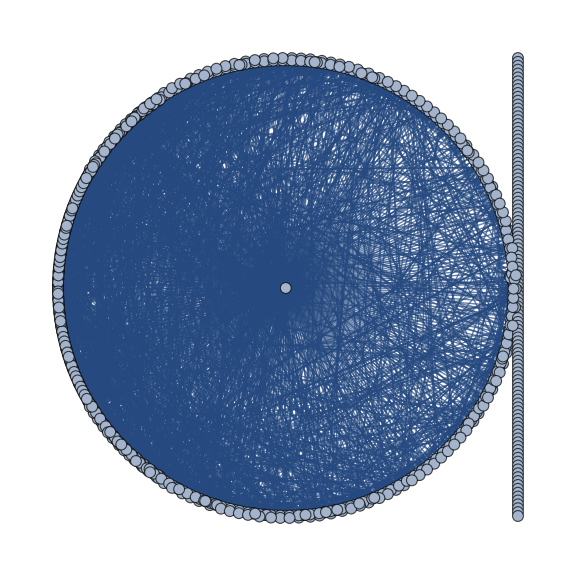

```mathematica
subG=Subgraph[sg,Keys@inDegree3OrMore,VertexLabels->Placed["Name",Tooltip],GraphLayout->"BalloonEmbedding",ImageSize->Large]
```

```mathematica
highlightedSubgraph=HighlightGraph[subG,{VertexList[subG],Property["WolframResearch",VertexSize->12]},VertexSize->Thread[Drop[VertexList[subG],1]->10 Rescale[Drop[DegreeCentrality[subG],1]]],ImageSize->Medium]
```

-Graphics-

```mathematica
comms=FindGraphCommunities[subG];
```

#### End of Graph

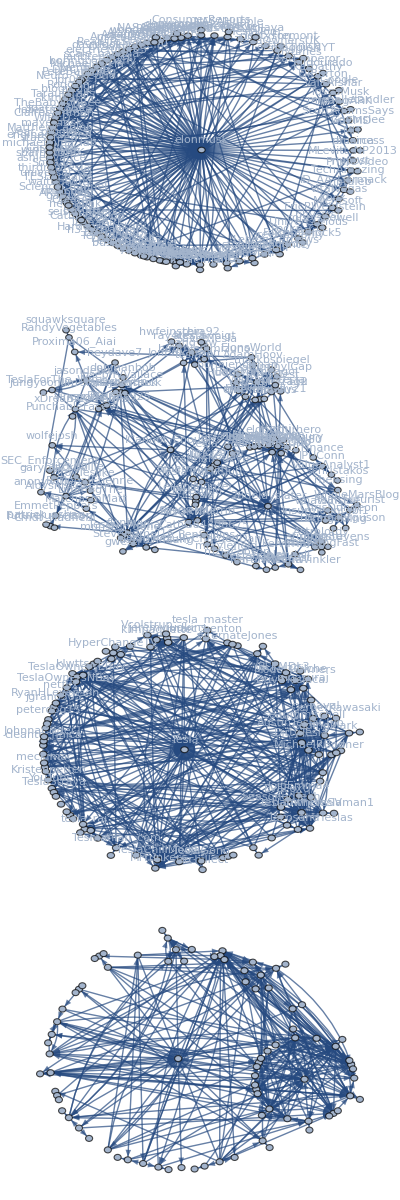

```mathematica
Column[Subgraph[subG,#,VertexLabels->Placed["Name",Above]]&/@FindGraphCommunities[subG][[1;;4]]]
```

### Visuals

```mathematica
Get[FileNameJoin[{Directory[],"muskTweetsWithUsermentions.mx"}]];
```

```mathematica
decAndAfterTweets=muskTweets[Select[#Date≥DateObject["Dec 2020","Second"]&],All]
```

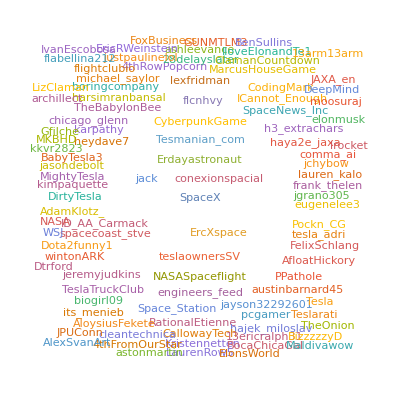

```mathematica
userMentionCloud=WordCloud[Normal[decAndAfterTweets[Flatten,"Usermentions"]]]
```

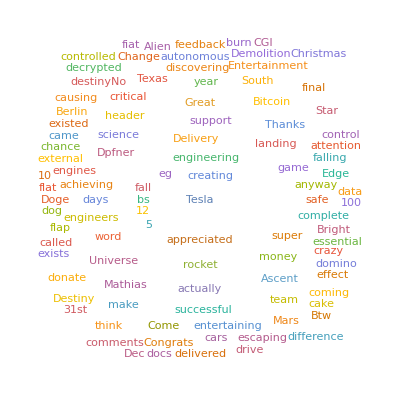

```mathematica
tweetTextCloud=decAndAfterTweets[Flatten/*StringSplit/*WordCloud,"Text",StringDelete[cleanText[#],"#"|"@"~~__]&]
```

```mathematica
cleanText[txt_String]:=StringTrim[StringReplace[DeleteStopwords[StringDelete[txt,{"&amp","&gt","'s",Except[{"@","#","_"},PunctuationCharacter],"RT","RN","JK","w/","http"~~Except[WhitespaceCharacter]..~~WhitespaceCharacter|EndOfString|PunctuationCharacter,s_/;!PrintableASCIIQ[s]}]],Repeated[WhitespaceCharacter]->" "]]
removeHTML[s_String]:=StringTrim[StringReplace[StringReplace[StringDelete[s,{"&amp","&gt","http"~~Except[WhitespaceCharacter]..~~WhitespaceCharacter|EndOfString|PunctuationCharacter,c_/;!PrintableASCIIQ[c]}],Except[{"@","#","_"},PunctuationCharacter]->" "],Repeated[WhitespaceCharacter]->" "]]
```

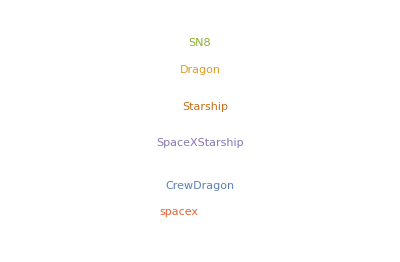

```mathematica
hashtagCloud=WordCloud[Normal[decAndAfterTweets[Flatten,"Hashtags"]]]
```

```mathematica
Grid[{{Labeled[Show[hashtagCloud,ImageSize->Scaled[0.9]],Style["Hashtags",Bold,"Text",Gray],Top],Labeled[Show[tweetTextCloud,ImageSize->Scaled[0.9]],Style["Text Content",Bold,"Text",Gray],Top]},{Labeled[Show[userMentionCloud,ImageSize->Scaled[0.9]],Style["User Mentions",Bold,"Text",Gray],Top],SpanFromAbove}},Dividers->Center,FrameStyle->Black,Alignment->{Top,Center},Frame->All,ItemSize->{{Scaled[.5],Scaled[.5]}}]
```

-Graphics-Hashtags | -Graphics-Text Content
-Graphics-User Mentions |

```mathematica
weeklyBuzz[decAndAfterTweets,1]
```

-Graphics-

```mathematica
weeklyTweets=weeklyBuzz[decAndAfterTweets,1];
weeklyRetweets=weeklyBuzz[decAndAfterTweets,2];
weeklyLikes=weeklyBuzz[decAndAfterTweets,3];
```

```mathematica
TabView[{"Tweets"->weeklyTweets,"Retweets"->weeklyRetweets,"Likes"->weeklyLikes},ControlPlacement->Bottom]
```

123

```mathematica
weeklyBuzzColor[tweetsData_,n_:1]:=Module[{daysOfWeek={Monday,Tuesday,Wednesday,Thursday,Friday,Saturday,Sunday},dayOfWeekCounts,dayOfWeekCountsSummary,dailyByHourTweets},dayOfWeekCounts=KeyTake[KeySort[GroupBy[#,First->Rest]]&/@GroupBy[{DateObject[#[[1]]]["DayName"],DateObject[#[[1]]]["Hour"],#[[2]],#[[3]]}&/@Normal[tweetsData[All,{"Date","RetweetCount","FavoriteCount"}]],First->Rest],daysOfWeek];
dayOfWeekCountsSummary=Merge[{Length/@#,Total/@#},Flatten]&/@dayOfWeekCounts;(AssociateTo[dayOfWeekCountsSummary[#],Table[i->{0,0,0},{i,Complement[Range[1,24],Keys[dayOfWeekCountsSummary[#]]]}]]&)/@Keys[dayOfWeekCountsSummary];
AssociateTo[dayOfWeekCountsSummary,Thread[Complement[daysOfWeek,Keys[dayOfWeekCountsSummary]]->Association[Table[i->{0,0,0},{i,24}]]]];
dailyByHourTweets=ArrayPlot[Map[#[[n]]&,((Values[KeySort[dayOfWeekCountsSummary[#]]]&)/@daysOfWeek),{2}],PlotRange->Full,ColorFunctionScaling->True,Mesh->True,Frame->True,FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->{{Table[{i,daysOfWeek[[i]]},{i,7}],None},{Range[24],None}},ImageSize->Full,PlotLabel->"elonmusk Tweets"<>Switch[n,1,"",2," Retweeted",3," Liked"]<>" ("<>DateString[tweetsData[Min,"Date"],{"MonthNameShort"," ","Day"}]<>" to "<>DateString[tweetsData[Max,"Date"],{"Day",", ","Year"}]<>")",PlotLegends->Placed[Automatic,Below],PlotTheme->"Marketing"]]
```

```mathematica
weeklyTweetsColor=weeklyBuzzColor[decAndAfterTweets,1];
weeklyRetweetsColor=weeklyBuzzColor[decAndAfterTweets,2];
weeklyLikesColor=weeklyBuzzColor[decAndAfterTweets,3];
```

```mathematica
TabView[{"Tweets"->weeklyTweetsColor,"Retweets"->weeklyRetweetsColor,"Likes"->weeklyLikesColor},ControlPlacement->Bottom]
```

123

```mathematica
Iconize[(cleanText[txt_String]:=StringTrim[StringReplace[DeleteStopwords[StringDelete[txt,{"&amp","&gt","'s",Except[{"@","#","_"},PunctuationCharacter],"RT","RN","JK","w/","http"~~Except[WhitespaceCharacter]..~~WhitespaceCharacter|EndOfString|PunctuationCharacter,s_/;!PrintableASCIIQ[s]}]],Repeated[WhitespaceCharacter]->" "]];
weeklyBuzzColor[tweetsData_,n_:1]:=Module[{daysOfWeek={Monday,Tuesday,Wednesday,Thursday,Friday,Saturday,Sunday},dayOfWeekCounts,dayOfWeekCountsSummary,dailyByHourTweets},dayOfWeekCounts=KeyTake[KeySort[GroupBy[#,First->Rest]]&/@GroupBy[{DateObject[#[[1]]]["DayName"],DateObject[#[[1]]]["Hour"],#[[2]],#[[3]]}&/@Normal[tweetsData[All,{"Date","RetweetCount","FavoriteCount"}]],First->Rest],daysOfWeek];
dayOfWeekCountsSummary=Merge[{Length/@#,Total/@#},Flatten]&/@dayOfWeekCounts;(AssociateTo[dayOfWeekCountsSummary[#],Table[i->{0,0,0},{i,Complement[Range[1,24],Keys[dayOfWeekCountsSummary[#]]]}]]&)/@Keys[dayOfWeekCountsSummary];
AssociateTo[dayOfWeekCountsSummary,Thread[Complement[daysOfWeek,Keys[dayOfWeekCountsSummary]]->Association[Table[i->{0,0,0},{i,24}]]]];
dailyByHourTweets=ArrayPlot[Map[#[[n]]&,((Values[KeySort[dayOfWeekCountsSummary[#]]]&)/@daysOfWeek),{2}],PlotRange->Full,ColorFunctionScaling->True,Mesh->True,Frame->True,FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],FrameTicks->{{Table[{i,daysOfWeek[[i]]},{i,7}],None},{Range[24],None}},ImageSize->Full,PlotLabel->"elonmusk Tweets"<>Switch[n,1,"",2," Retweeted",3," Liked"]<>" ("<>DateString[tweetsData[Min,"Date"],{"MonthNameShort"," ","Day"}]<>" to "<>DateString[tweetsData[Max,"Date"],{"Day",", ","Year"}]<>")",PlotLegends->Placed[Automatic,Below],ColorFunction->ColorData[{"SandyTerrain","Reverse"}],ColorFunctionScaling->True]];
panel[handle_String]:=Module[{begin,end,twitter,tweets,hashtagCloud,weeklyBuzz,tweetSentiments,favouriteCount,retweetCount},begin=DateObject[PreviousDate["Week"],TimeObject[{00}]];
end=DatePlus[begin,{1,"Week"}];
twitter=ServiceConnect["Twitter"];
tweets=twitter["TweetList","Username"->handle,"Elements"->"FullData",MaxItems->500][Select[#Date≥begin&&#Date≤end&],All];
hashtagCloud=WordCloud[Normal[tweets[Flatten,"Hashtags"]]];
weeklyBuzz=weeklyBuzzColor[tweets,1];
tweetSentiments=PieChart[Merge[{<|"Negative"->0,"Neutral"->0,"Positive"->0|>,Counts[Classify["Sentiment"][tweets[All,#Text&]]]},Total],PlotTheme->{"Web","Square"},ChartStyle->{RGBColor[0.8115292,0.2810584,0.1],GrayLevel[0.5],RGBColor[0.,0.4,0.]},ChartLegends->Placed[{"Negative","Neutral","Positive"},Below],PlotLabel->"Tweet Sentiment Analysis",ImageSize->Small];
favouriteCount=Histogram[Normal[tweets[All,"FavoriteCount"]],{1},"Count",PlotTheme->{"Web","Square"},PlotLabel->"Favorite Count",FrameLabel->{{"Number of Tweets",None},{"Number of Likes",None}},Frame->{{True,False},{True,False}},ImageSize->Small];
retweetCount=Histogram[Normal[tweets[All,"RetweetCount"]],{1},"Count",PlotTheme->{"Web","Square"},PlotLabel->"Retweet Count",FrameLabel->{{"Number of Tweets",None},{"Number of Retweets",None}},Frame->{{True,False},{True,False}},ImageSize->Small];
Rasterize@Panel[Grid[{{weeklyBuzz,SpanFromLeft,Column[{" ",Show[hashtagCloud,ImageSize->Scaled[0.95]]," ",Style["Hashtags","Text",14,Gray]},Alignment->Center]},{Show[favouriteCount,ImageSize->Scaled[0.9]],Show[retweetCount,ImageSize->Scaled[0.9]],Show[tweetSentiments,ImageSize->Scaled[0.9]]}},ItemSize->{{Scaled[0.3],Scaled[0.3],Scaled[0.3]}}],Style[handle~~" Tweets at a Glance","Subsubtitle"],Bottom]];
panel[#handle]&),"FormActionCode"]
```

```mathematica
panel[#handle]&
```

```mathematica
CloudDeploy@FormPage[{"handle","Twitter Handle"}->"String",panel[Slot["handle"]]&,AppearanceRules-><|"Title"->"Tweets Last Week","Description"->"Weekly report on tweets from a particular account"|>]
```

CloudObject[https://www.wolframcloud.com/obj/7a206e55-e37b-4260-9482-4d0a9ce9f982]